```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
(*calculated already unified*)
mH=126.22136632802759*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=125.38*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.93*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*https://en.wikipedia.org/wiki/Stefan%E2%80%93Boltzmann_law*)
σ=5.670374419*10^(-5)
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
```

0.0000567037

```mathematica
(*Neutrino mass from Symmetry breaking theory of weak and electromagnetic quantum curvatures:1.9964323595279435*^-32*)
mnue=Sqrt[e]*me;
```

```mathematica
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
N[Log[10,N0]]
```

23.7798

```mathematica
(*monster group F24 very near Avagodro's number*)
```

```mathematica
(*https://brauer.maths.qmul.ac.uk/Atlas/v3/spor/F24/*)
```

```mathematica
nf24=1255205709190661721292800
```

1255205709190661721292800

```mathematica
(* factor near 2: Spin2 geon*)
```

```mathematica
nf24/N0
```

2.08432

```mathematica
(* 52/9 rational alpha residue*)
```

```mathematica
(2.084318117450748/2-1)/((5+7/9)*α)
```

0.999919

```mathematica
N[Log[10,nf24]]
```

24.0987

```mathematica
(* Geon / boson thermodynamic constant*)
```

```mathematica
nf24*kb*G
```

11.5637

```mathematica
nf24*kb*G/c^2
```

1.28663×10^-20

```mathematica
1.2866311273544106*^-20/mhiggs
```

57.5648

```mathematica
(* finding the nearest rational constant*)
```

```mathematica
Table[{i,T}/.Solve[nf24*kb*T==i,T][[1]],{i,1,25,0.5}]
```

{{1.,5.77031×10^-9},{1.5,8.65546×10^-9},{2.,1.15406×10^-8},{2.5,1.44258×10^-8},{3.,1.73109×10^-8},{3.5,2.01961×10^-8},{4.,2.30812×10^-8},{4.5,2.59664×10^-8},{5.,2.88515×10^-8},{5.5,3.17367×10^-8},{6.,3.46218×10^-8},{6.5,3.7507×10^-8},{7.,4.03922×10^-8},{7.5,4.32773×10^-8},{8.,4.61625×10^-8},{8.5,4.90476×10^-8},{9.,5.19328×10^-8},{9.5,5.48179×10^-8},{10.,5.77031×10^-8},{10.5,6.05882×10^-8},{11.,6.34734×10^-8},{11.5,6.63585×10^-8},{12.,6.92437×10^-8},{12.5,7.21288×10^-8},{13.,7.5014×10^-8},{13.5,7.78992×10^-8},{14.,8.07843×10^-8},{14.5,8.36695×10^-8},{15.,8.65546×10^-8},{15.5,8.94398×10^-8},{16.,9.23249×10^-8},{16.5,9.52101×10^-8},{17.,9.80952×10^-8},{17.5,1.0098×10^-7},{18.,1.03866×10^-7},{18.5,1.06751×10^-7},{19.,1.09636×10^-7},{19.5,1.12521×10^-7},{20.,1.15406×10^-7},{20.5,1.18291×10^-7},{21.,1.21176×10^-7},{21.5,1.24062×10^-7},{22.,1.26947×10^-7},{22.5,1.29832×10^-7},{23.,1.32717×10^-7},{23.5,1.35602×10^-7},{24.,1.38487×10^-7},{24.5,1.41373×10^-7},{25.,1.44258×10^-7}}

```mathematica
(* temerature at rational constant:23/2=11.5*)
```

```mathematica
T0=6.635853976816946*^-8
```

6.63585×10^-8

```mathematica
Solve[Sum[(x*P)^n,{n,0,Infinity}]==11.5,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.913043/P}}

```mathematica
Rationalize[0.9130434782608695]
```

21/23

```mathematica
Sum[((21/23)*P)^n,{n,0,Infinity}]
```

-23/(-23+21 P)

```mathematica
(* near unitary pressure at T=G in F24 group*)
```

```mathematica
p0=P/.Solve[-23/(-23+21 P)-nf24*kb*G==0,P][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.00052

```mathematica
Clear[V0,T1]
```

```mathematica
(* p*v volume at T=G*)
```

```mathematica
V0=V0/.Solve[p0*V0==nf24*kb*G,V0][[1]]
```

11.5576

```mathematica
(* T1 temperature at first term of thermodyamic sequence*)
```

```mathematica
T1=T1/.Solve[p0*V0==N0*kb*T1+Sum[((21/23)*p0)^n,{n,1,Infinity}],T1][[1]]/.N0->6.02214076*10^23
```

1.20272×10^-8

```mathematica
(* three temperatures*)
```

```mathematica
tt={G,T0,T1}
```

{6.67259×10^-8,6.63585×10^-8,1.20272×10^-8}

```mathematica
tt/G
```

{1.,0.994494,0.180247}

```mathematica
(*R*T values ; energy*)
```

```mathematica
ei=N0*kb*tt
```

{5.54794,5.51739,1.}

```mathematica
(*mass at R*T values*)
```

```mathematica
mm=N0*kb*tt/c^2
```

{6.17291×10^-21,6.13893×10^-21,1.11265×10^-21}

```mathematica
mr=mm/mhiggs
```

{27.618,27.466,4.97807}

```mathematica
(*quantum radii*)
```

```mathematica
r=2*Pi*hbar/(mm*c)
```

{3.58052×10^-17,3.60034×10^-17,1.98645×10^-16}

```mathematica
vv=4*Pi*r^3/3
```

{1.92276×10^-49,1.95487×10^-49,3.28337×10^-47}

```mathematica
.10(*hyper-Pressures*)
```

.10

```mathematica
ph=Table[ei[[i]]/vv[[i]],{i,3}]
```

{2.8854×10^49,2.82238×10^49,3.04565×10^46}

```mathematica
(*Weeks Hyperbolic 3 manifold*)
```

```mathematica
Discriminant[x^3-x-1,x]
```

-23

```mathematica
V3=vw*r[[1]]^3
```

4.32727×10^-50

```mathematica
(*relative hyper-energies to Weeks Boson*)
```

```mathematica
ph*V3
```

{1.24859,1.22132,0.00131793}

```mathematica
vv[[1]]-V3
```

1.49003×10^-49

```mathematica
vr=vv/V3
```

{4.44336,4.51757,758.763}

```mathematica
vr.mr/2^12
```

0.982416

```mathematica
vr.mm/2^12
```

2.1958×10^-22

```mathematica
2.195798480278627*^-22/mhiggs
```

0.982416

```mathematica
-tt[[1]]*N0*kb+tt[[2]]*N0*kb+(tt[[1]]-tt[[2]])*N0*kb//Chop
```

0

```mathematica
pw[x_]=4*ExpandAll[(x-tt[[1]]*N0*kb)*(x+tt[[2]]*N0*kb)*(x+(tt[[1]]-tt[[2]])*N0*kb)]//Chop
```

4 (-0.934963-30.6111 x+x^3)

```mathematica
gg=CoefficientList[pw[x],x]
```

{-3.73985,-122.444,0,4}

```mathematica
g2=-gg[[2]]
g3=-gg[[1]]
```

122.444

3.73985

```mathematica
j=g2^3/(g2^3-27*g3^2)
```

1.00021

```mathematica
Ng[i_]:=nf24/(Exp[ei[[i]]/5.54794]-1)
```

```mathematica
Table[Ng[i],{i,3}]/N0
```

{1.21303,1.22365,10.5528}

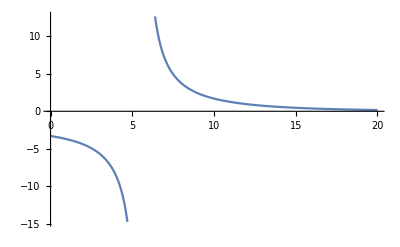

```mathematica
Plot[(nf24/(Exp[(x-5.54794)/5.54794]-1))/N0,{x,0,20}]
```

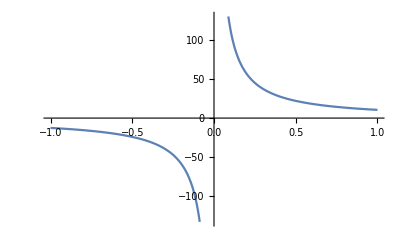

```mathematica
Plot[(nf24/(Exp[x/5.54794]-1))/N0,{x,-1,1}]
```

```mathematica
(*Generalized Finsler-Klein-Gorden energy of geon*)
```

```mathematica
eg=Table[x/.Solve[D[(nf24/(Exp[x/5.54794]-1)),{x,2}]==(6.172911498404289*^-21*c/hbar)^i*(nf24/(Exp[x/5.54794]-1)),x][[1]]/. C[1]->0//Chop,{i,0,10}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{-1.33334,-3.37596×10^-9,0,0,0,0,0,0,0,0,0}

```mathematica
-1.3333395816772986/5.54794
```

-0.240331

```mathematica
-3.375964530271661*^-9/G
```

-0.0505945

```mathematica
eg=Table[x/.Solve[D[(nf24/(Exp[x/5.54794]-1)),{x,1}]==(6.172911498404289*^-21*c/hbar)^i*(nf24/(Exp[x/5.54794]-1)),x]/. C[1]->0//Chop,{i,0,10}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{-0.919426},x,x,x,x,x,x,x,x,x,x}

```mathematica
eg=Table[x/.Solve[D[(nf24/(Exp[x/5.54794]-1)),{x,3}]==(6.172911498404289*^-21*c/hbar)^i*(nf24/(Exp[x/5.54794]-1)),x]/. C[1]->0//Chop,{i,0,10}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{-1.72755,0.847579-1.65821 ⅈ,0.847579+1.65821 ⅈ},{-3.24568×10^-6,1.62284×10^-6-2.81084×10^-6 ⅈ,1.62284×10^-6+2.81084×10^-6 ⅈ},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Clear[pw]
```

```mathematica
kg={-1.7275518841749502,0.8475788161087411-1.658212156280363 ⅈ,0.8475788161087411+1.658212156280363 ⅈ}
```

{-1.72755,0.847579-1.65821 ⅈ,0.847579+1.65821 ⅈ}

```mathematica
pw[x_]=ExpandAll[4*Product[(x-kg[[i]]),{i,3}]]//Chop
```

23.965+2.15834 x+0.129577 x^2+4 x^3

```mathematica
gg=CoefficientList[pw[x],x]
```

{23.965,2.15834,0.129577,4}

```mathematica
g2=-gg[[2]]
g3=-gg[[1]]
```

-2.15834

-23.965

```mathematica
j=g2^3/(g2^3-27*g3^2)
```

0.000647976

```mathematica
(*photon/ black body flux *)
```

```mathematica
Er=V0*σ*G^4
```

1.29914×10^-32

```mathematica
(* mass of flux*)
```

```mathematica
Er/c^2
```

1.44549×10^-53

```mathematica
(* phontonic 1/3 energy*)
```

```mathematica
p0*V0/3
```

3.85455

```mathematica
(p0*V0/3)/c^2
```

4.28877×10^-21

```mathematica
((p0*V0/3)/c^2)/mhiggs
```

19.1883